```mathematica
data =Import["/Users/jdyeakel/Dropbox/PostDoc/2020_Sevilleta2/data/scaled_eigenvecs.csv"]
```

{{14.303,1.31753,0.0425535},{14.3467,1.59126,0.26872},{14.4015,1.52715,0.304259},{14.4269,1.62764,0.354608},{14.4758,1.57557,0.329049},{14.5196,1.49517,0.311338},{14.4963,1.53032,0.331442},{14.4647,1.54008,0.371006},{14.4427,1.54616,0.34136},{14.3676,1.5466,0.347188},{14.3378,1.55756,0.322911},{14.1766,1.54502,0.362971},{13.8417,1.51782,0.374995},{13.7096,1.50887,0.346403},{13.1547,1.47023,0.356304},{12.7933,1.44181,0.342585},{12.1716,1.39086,0.357716},{11.7169,1.35257,0.352161},{11.4653,1.3313,0.353265},{10.9445,1.28627,0.375988},{10.2491,1.22481,0.361345},{10.2488,1.22479,0.337674},{9.5282,1.15939,0.334502},{9.06394,1.11678,0.346075},{8.32808,1.04852,0.342324},{7.855,1.00414,0.349301},{7.85463,1.0041,0.363359},{7.07164,0.929313,0.370315},{6.64655,0.888319,0.37196},{6.37754,0.862213,0.347024},{5.88898,0.814402,0.337514},{5.40691,0.766869,0.365734},{4.48166,0.675011,0.387029},{4.22826,0.649695,0.361182},{4.05752,0.632516,0.37251},{3.38343,0.564327,0.337161},{2.63391,0.488041,0.362675},{2.43603,0.467798,0.355606},{2.43583,0.467777,0.363127},{2.11972,0.435092,0.371361},{1.94674,0.417117,0.3479},{1.80738,0.402564,0.351293},{1.80734,0.402559,0.355425},{1.80729,0.402554,0.361306},{1.80723,0.402548,0.394405},{1.80716,0.40254,0.355568},{1.80709,0.402532,0.348769},{12.0132,4.43228,0.454326},{11.1669,5.13753,0.426291},{9.09323,6.70002,0.458205},{6.56286,8.44198,0.463039},{6.54896,8.45111,0.436667},{6.53107,8.46246,0.421428},{5.40386,9.15066,0.42263},{4.26721,9.81914,0.387325},{3.78098,10.1091,0.41045},{2.75035,10.6818,0.410554},{2.23638,10.9691,0.424207},{0.332058,11.9513,0.396052},{-0.741212,12.4957,0.394846},{-1.83536,13.0349,0.413028},{-2.97781,13.5755,0.435946},{-4.10521,14.0891,0.402199},{-5.26697,14.5953,0.384328},{-6.31984,15.0381,0.380533},{-7.7184,15.606,0.426979},{-8.64012,15.9591,0.39603},{-9.50843,16.2752,0.390007},{-10.3305,16.5583,0.410777},{-11.09,16.8049,0.390271},{-11.8029,17.0219,0.378542},{-12.0625,17.0973,0.40556},{-12.6746,17.2571,0.37616},{-13.2437,17.3933,0.361612},{-13.7734,17.5083,0.406756},{-14.2635,17.6034,0.348384},{-14.7351,17.684,0.397975},{-15.1645,17.7471,0.356407},{-15.5858,17.7988,0.365996},{-15.9708,17.8366,0.384313},{-16.3204,17.8623,0.36159},{-16.6388,17.8776,0.386199},{-17.1738,17.8893,0.376951},{-17.329,17.8891,0.391741},{-17.4759,17.8852,0.396368},{-17.6127,17.8779,0.365006},{-17.7406,17.8677,0.422677},{-17.8601,17.8549,0.360393},{-17.972,17.8399,0.360123},{-17.9723,17.8398,0.361188},{-17.9725,17.8398,0.36295},{-17.9729,17.8397,0.374937},{-17.9732,17.8396,0.37784},{13.4205,1.12335,0.662526},{12.7629,0.936197,0.760748},{12.1487,0.763901,0.775959},{10.5977,0.371286,0.70073},{9.64524,0.161994,0.717956},{9.6331,0.159215,0.762918},{8.72928,-0.0436071,0.667681},{7.81294,-0.244249,0.68684},{6.8584,-0.447914,0.685812},{6.38636,-0.547231,0.668354},{5.50442,-0.728117,0.663355},{4.1002,-1.01234,0.661381},{3.13074,-1.20525,0.689153},{2.12942,-1.40127,0.663038},{0.770812,-1.66319,0.720157},{0.216342,-1.76799,0.681461},{-1.14771,-2.02266,0.668674},{-1.65203,-2.11505,0.683563},{-2.90311,-2.34118,0.703759},{-3.71381,-2.48519,0.657277},{-3.71664,-2.48568,0.694879},{-4.92873,-2.69353,0.7185},{-5.54531,-2.79765,0.6391},{-6.59048,-2.97068,0.71389},{-6.8512,-3.0131,0.67813},{-7.44228,-3.10735,0.692016},{-8.35629,-3.25028,0.655677},{-8.87067,-3.32917,0.71269},{-9.06284,-3.35804,0.71784},{-9.55193,-3.42995,0.715237},{-9.97165,-3.49035,0.734542},{-10.5034,-3.56521,0.622298},{-10.745,-3.59847,0.680171},{-11.0553,-3.6402,0.662239},{-11.3342,-3.67683,0.656353},{-11.8289,-3.74024,0.62344},{-11.9742,-3.75843,0.645673},{-12.1108,-3.77509,0.6486},{-12.1116,-3.77519,0.627616},{-12.3446,-3.80212,0.684605},{-12.454,-3.81444,0.676606},{-12.5578,-3.82579,0.68944},{-12.5581,-3.82581,0.688399},{-12.5583,-3.82584,0.627842},{-12.5586,-3.82587,0.672878},{-12.5589,-3.8259,0.622115},{14.5012,1.32561,0.935939},{14.4772,1.3111,0.930313},{14.4542,1.4045,0.974258},{14.4207,1.39639,1.0543},{14.2282,1.32534,1.07487},{14.1507,1.31652,1.07509},{14.0545,1.30747,1.06393},{13.714,1.26918,0.938523},{13.9417,1.29465,1.00071},{13.3602,1.23009,1.02091},{13.3936,1.22914,0.982548},{12.4634,1.13256,0.993809},{11.8739,1.06979,1.05633},{11.57,1.03749,1.04797},{11.459,1.0258,1.13315},{10.6032,0.935752,1.02018},{9.57432,0.827791,1.06753},{9.28872,0.79791,1.03461},{9.18464,0.786997,1.06314},{8.67645,0.7338,1.00287},{7.58795,0.619905,1.06988},{7.85994,0.648395,0.98009},{7.82291,0.644524,1.11857},{7.46108,0.606653,0.97869},{6.81488,0.538991,1.05647},{7.13508,0.572523,1.12622},{6.19534,0.474101,1.09039},{6.25103,0.479947,1.10948},{5.82219,0.435015,0.988973},{4.89503,0.337808,1.08036},{5.10375,0.359701,1.06244},{5.3371,0.384167,0.929648},{4.9313,0.341618,1.19314},{4.52357,0.29883,1.01288},{4.71498,0.31892,1.01123},{4.49857,0.296201,1.04184},{4.4413,0.290189,1.11676},{4.41747,0.287685,1.04986},{4.2652,0.271682,1.07209},{4.19773,0.264591,1.11435},{4.14692,0.259249,1.13576},{4.0252,0.246446,1.02601},{4.08163,0.252383,1.05927},{4.04499,0.248528,1.13021},{3.97887,0.241572,1.1797},{3.97844,0.241526,1.12916},{12.5359,0.156326,0.897075},{11.8342,-0.215921,0.884181},{9.09298,-1.53026,0.855772},{9.07691,-1.53729,0.977943},{7.92317,-2.02442,0.999745},{7.9087,-2.03049,0.916847},{6.92579,-2.43336,0.870871},{5.92122,-2.83346,0.895829},{5.49612,-3.00242,0.895322},{5.02158,-3.18702,0.808351},{3.7525,-3.65728,0.855603},{2.35665,-4.16499,0.827794},{1.37921,-4.51442,0.764328},{0.417318,-4.85087,0.69735},{-0.968871,-5.3263,0.734059},{-1.56003,-5.52012,0.78659},{-2.87452,-5.95013,0.785879},{-3.71098,-6.21616,0.697818},{-4.49686,-6.45959,0.698469},{-5.26481,-6.69165,0.721829},{-5.55996,-6.77992,0.698401},{-6.64456,-7.08876,0.719439},{-6.91078,-7.16384,0.694695},{-7.50157,-7.32276,0.641761},{-7.82872,-7.40724,0.625063},{-8.64944,-7.61471,0.594163},{-9.17116,-7.74158,0.651644},{-9.69893,-7.865,0.642178},{-10.168,-7.97046,0.634315},{-10.448,-8.03063,0.618599},{-11.4184,-8.23046,0.602215},{-11.5823,-8.26262,0.61157},{-11.9782,-8.33652,0.594478},{-12.3451,-8.40144,0.639858},{-12.6798,-8.45741,0.562974},{-13.4259,-8.57484,0.598125},{-13.4266,-8.57494,0.617421},{-13.5648,-8.59402,0.554552},{-13.7102,-8.6127,0.531807},{-13.8468,-8.62887,0.569449},{-13.9751,-8.64276,0.614337},{-14.0956,-8.65459,0.521763},{-14.0958,-8.65461,0.612029},{-14.0961,-8.65463,0.477389},{-14.0964,-8.65465,0.565411},{-14.0968,-8.65467,0.562057},{14.3368,1.40071,1.31957},{14.2012,1.35818,1.33524},{14.0951,1.32809,1.33097},{13.4953,1.16867,1.38326},{13.4758,1.00616,1.36981},{12.662,1.0145,1.33725},{12.6532,1.0129,1.37603},{11.6548,0.845664,1.31906},{11.3328,0.791381,1.26283},{11.0079,0.744752,1.34454},{10.0129,0.610111,1.33398},{9.6462,0.558526,1.34394},{8.50665,0.398732,1.38219},{8.48334,0.395555,1.44346},{6.77272,0.165696,1.45319},{5.03746,-0.0634617,1.44125},{5.90776,0.0511603,1.37658},{3.85004,-0.2182,1.35196},{2.54858,-0.38594,1.50585},{1.69229,-0.495161,1.33846},{1.83076,-0.477636,1.43917},{0.627452,-0.628835,1.45283},{0.298811,-0.669739,1.37564},{0.297012,-0.669961,1.44647},{-0.170759,-0.727156,1.45717},{-0.435353,-0.759222,1.3843},{-0.545991,-0.772514,1.38012},{-0.926437,-0.817845,1.40782},{-0.943377,-0.819845,1.4259},{-1.50955,-0.885845,1.45475},{-1.27207,-0.858363,1.42838},{-1.37918,-0.870802,1.49111},{-2.14666,-0.95857,1.42742},{-2.04567,-0.947116,1.39211},{-2.35561,-0.982078,1.4326},{-2.42981,-0.990352,1.39964},{-2.78198,-1.02917,1.42455},{-2.57861,-1.00683,1.47071},{-2.78215,-1.02919,1.4673},{-2.88749,-1.04058,1.5216},{-2.88798,-1.04063,1.61873},{-2.88807,-1.04064,1.37297},{-3.08931,-1.0619,1.48709},{-3.08951,-1.06192,1.49837},{-3.08962,-1.06193,1.43606},{-3.09002,-1.06197,1.49696},{11.8433,-0.891989,0.169771},{9.70595,-2.11224,0.190113},{8.67138,-2.69942,0.210225},{7.53834,-3.29389,0.235715},{7.53267,-3.29685,0.252285},{7.5252,-3.3006,0.255261},{6.87881,-3.63101,0.254695},{6.87593,-3.6324,0.288912},{6.02328,-4.02973,0.294901},{5.28175,-4.37475,0.295463},{4.58823,-4.68942,0.309746},{3.1933,-5.30445,0.332167},{2.751,-5.50149,0.339786},{1.43739,-6.05089,0.324648},{0.148348,-6.58761,0.317155},{-0.356431,-6.78611,0.343633},{-1.64276,-7.29527,0.342634},{-2.43557,-7.59849,0.345802},{-2.94174,-7.78249,0.346584},{-3.75838,-8.07847,0.347851},{-4.39553,-8.30787,0.359429},{-5.4974,-8.68087,0.368146},{-5.79058,-8.77963,0.358209},{-6.1563,-8.89435,0.372441},{-7.4495,-9.29184,0.365599},{-7.80269,-9.39535,0.38023},{-8.3208,-9.54358,0.380237},{-8.66542,-9.63626,0.398273},{-9.42864,-9.83376,0.382322},{-10.2969,-10.0472,0.385169},{-10.4879,-10.0917,0.378035},{-11.1904,-10.2465,0.384532},{-11.3369,-10.2768,0.398859},{-11.9896,-10.4039,0.387506},{-12.0945,-10.4228,0.395529},{-12.6605,-10.5179,0.397908},{-12.8139,-10.5419,0.410513},{-12.9748,-10.565,0.426982},{-13.1065,-10.5821,0.412288},{-13.2472,-10.5986,0.385527},{-13.355,-10.6097,0.425223},{-13.4731,-10.6203,0.415227},{-13.4733,-10.6204,0.431731},{-13.4736,-10.6204,0.419089},{-13.4738,-10.6204,0.426231},{-13.4741,-10.6204,0.425728}}

```mathematica
interpolatedata={{#[[1]],#[[2]]},#[[3]]}&/@data;
```

```mathematica
interpolatedata
```

{{{14.303,1.31753},0.0425535},{{14.3467,1.59126},0.26872},{{14.4015,1.52715},0.304259},{{14.4269,1.62764},0.354608},{{14.4758,1.57557},0.329049},{{14.5196,1.49517},0.311338},{{14.4963,1.53032},0.331442},{{14.4647,1.54008},0.371006},{{14.4427,1.54616},0.34136},{{14.3676,1.5466},0.347188},{{14.3378,1.55756},0.322911},{{14.1766,1.54502},0.362971},{{13.8417,1.51782},0.374995},{{13.7096,1.50887},0.346403},{{13.1547,1.47023},0.356304},{{12.7933,1.44181},0.342585},{{12.1716,1.39086},0.357716},{{11.7169,1.35257},0.352161},{{11.4653,1.3313},0.353265},{{10.9445,1.28627},0.375988},{{10.2491,1.22481},0.361345},{{10.2488,1.22479},0.337674},{{9.5282,1.15939},0.334502},{{9.06394,1.11678},0.346075},{{8.32808,1.04852},0.342324},{{7.855,1.00414},0.349301},{{7.85463,1.0041},0.363359},{{7.07164,0.929313},0.370315},{{6.64655,0.888319},0.37196},{{6.37754,0.862213},0.347024},{{5.88898,0.814402},0.337514},{{5.40691,0.766869},0.365734},{{4.48166,0.675011},0.387029},{{4.22826,0.649695},0.361182},{{4.05752,0.632516},0.37251},{{3.38343,0.564327},0.337161},{{2.63391,0.488041},0.362675},{{2.43603,0.467798},0.355606},{{2.43583,0.467777},0.363127},{{2.11972,0.435092},0.371361},{{1.94674,0.417117},0.3479},{{1.80738,0.402564},0.351293},{{1.80734,0.402559},0.355425},{{1.80729,0.402554},0.361306},{{1.80723,0.402548},0.394405},{{1.80716,0.40254},0.355568},{{1.80709,0.402532},0.348769},{{12.0132,4.43228},0.454326},{{11.1669,5.13753},0.426291},{{9.09323,6.70002},0.458205},{{6.56286,8.44198},0.463039},{{6.54896,8.45111},0.436667},{{6.53107,8.46246},0.421428},{{5.40386,9.15066},0.42263},{{4.26721,9.81914},0.387325},{{3.78098,10.1091},0.41045},{{2.75035,10.6818},0.410554},{{2.23638,10.9691},0.424207},{{0.332058,11.9513},0.396052},{{-0.741212,12.4957},0.394846},{{-1.83536,13.0349},0.413028},{{-2.97781,13.5755},0.435946},{{-4.10521,14.0891},0.402199},{{-5.26697,14.5953},0.384328},{{-6.31984,15.0381},0.380533},{{-7.7184,15.606},0.426979},{{-8.64012,15.9591},0.39603},{{-9.50843,16.2752},0.390007},{{-10.3305,16.5583},0.410777},{{-11.09,16.8049},0.390271},{{-11.8029,17.0219},0.378542},{{-12.0625,17.0973},0.40556},{{-12.6746,17.2571},0.37616},{{-13.2437,17.3933},0.361612},{{-13.7734,17.5083},0.406756},{{-14.2635,17.6034},0.348384},{{-14.7351,17.684},0.397975},{{-15.1645,17.7471},0.356407},{{-15.5858,17.7988},0.365996},{{-15.9708,17.8366},0.384313},{{-16.3204,17.8623},0.36159},{{-16.6388,17.8776},0.386199},{{-17.1738,17.8893},0.376951},{{-17.329,17.8891},0.391741},{{-17.4759,17.8852},0.396368},{{-17.6127,17.8779},0.365006},{{-17.7406,17.8677},0.422677},{{-17.8601,17.8549},0.360393},{{-17.972,17.8399},0.360123},{{-17.9723,17.8398},0.361188},{{-17.9725,17.8398},0.36295},{{-17.9729,17.8397},0.374937},{{-17.9732,17.8396},0.37784},{{13.4205,1.12335},0.662526},{{12.7629,0.936197},0.760748},{{12.1487,0.763901},0.775959},{{10.5977,0.371286},0.70073},{{9.64524,0.161994},0.717956},{{9.6331,0.159215},0.762918},{{8.72928,-0.0436071},0.667681},{{7.81294,-0.244249},0.68684},{{6.8584,-0.447914},0.685812},{{6.38636,-0.547231},0.668354},{{5.50442,-0.728117},0.663355},{{4.1002,-1.01234},0.661381},{{3.13074,-1.20525},0.689153},{{2.12942,-1.40127},0.663038},{{0.770812,-1.66319},0.720157},{{0.216342,-1.76799},0.681461},{{-1.14771,-2.02266},0.668674},{{-1.65203,-2.11505},0.683563},{{-2.90311,-2.34118},0.703759},{{-3.71381,-2.48519},0.657277},{{-3.71664,-2.48568},0.694879},{{-4.92873,-2.69353},0.7185},{{-5.54531,-2.79765},0.6391},{{-6.59048,-2.97068},0.71389},{{-6.8512,-3.0131},0.67813},{{-7.44228,-3.10735},0.692016},{{-8.35629,-3.25028},0.655677},{{-8.87067,-3.32917},0.71269},{{-9.06284,-3.35804},0.71784},{{-9.55193,-3.42995},0.715237},{{-9.97165,-3.49035},0.734542},{{-10.5034,-3.56521},0.622298},{{-10.745,-3.59847},0.680171},{{-11.0553,-3.6402},0.662239},{{-11.3342,-3.67683},0.656353},{{-11.8289,-3.74024},0.62344},{{-11.9742,-3.75843},0.645673},{{-12.1108,-3.77509},0.6486},{{-12.1116,-3.77519},0.627616},{{-12.3446,-3.80212},0.684605},{{-12.454,-3.81444},0.676606},{{-12.5578,-3.82579},0.68944},{{-12.5581,-3.82581},0.688399},{{-12.5583,-3.82584},0.627842},{{-12.5586,-3.82587},0.672878},{{-12.5589,-3.8259},0.622115},{{14.5012,1.32561},0.935939},{{14.4772,1.3111},0.930313},{{14.4542,1.4045},0.974258},{{14.4207,1.39639},1.0543},{{14.2282,1.32534},1.07487},{{14.1507,1.31652},1.07509},{{14.0545,1.30747},1.06393},{{13.714,1.26918},0.938523},{{13.9417,1.29465},1.00071},{{13.3602,1.23009},1.02091},{{13.3936,1.22914},0.982548},{{12.4634,1.13256},0.993809},{{11.8739,1.06979},1.05633},{{11.57,1.03749},1.04797},{{11.459,1.0258},1.13315},{{10.6032,0.935752},1.02018},{{9.57432,0.827791},1.06753},{{9.28872,0.79791},1.03461},{{9.18464,0.786997},1.06314},{{8.67645,0.7338},1.00287},{{7.58795,0.619905},1.06988},{{7.85994,0.648395},0.98009},{{7.82291,0.644524},1.11857},{{7.46108,0.606653},0.97869},{{6.81488,0.538991},1.05647},{{7.13508,0.572523},1.12622},{{6.19534,0.474101},1.09039},{{6.25103,0.479947},1.10948},{{5.82219,0.435015},0.988973},{{4.89503,0.337808},1.08036},{{5.10375,0.359701},1.06244},{{5.3371,0.384167},0.929648},{{4.9313,0.341618},1.19314},{{4.52357,0.29883},1.01288},{{4.71498,0.31892},1.01123},{{4.49857,0.296201},1.04184},{{4.4413,0.290189},1.11676},{{4.41747,0.287685},1.04986},{{4.2652,0.271682},1.07209},{{4.19773,0.264591},1.11435},{{4.14692,0.259249},1.13576},{{4.0252,0.246446},1.02601},{{4.08163,0.252383},1.05927},{{4.04499,0.248528},1.13021},{{3.97887,0.241572},1.1797},{{3.97844,0.241526},1.12916},{{12.5359,0.156326},0.897075},{{11.8342,-0.215921},0.884181},{{9.09298,-1.53026},0.855772},{{9.07691,-1.53729},0.977943},{{7.92317,-2.02442},0.999745},{{7.9087,-2.03049},0.916847},{{6.92579,-2.43336},0.870871},{{5.92122,-2.83346},0.895829},{{5.49612,-3.00242},0.895322},{{5.02158,-3.18702},0.808351},{{3.7525,-3.65728},0.855603},{{2.35665,-4.16499},0.827794},{{1.37921,-4.51442},0.764328},{{0.417318,-4.85087},0.69735},{{-0.968871,-5.3263},0.734059},{{-1.56003,-5.52012},0.78659},{{-2.87452,-5.95013},0.785879},{{-3.71098,-6.21616},0.697818},{{-4.49686,-6.45959},0.698469},{{-5.26481,-6.69165},0.721829},{{-5.55996,-6.77992},0.698401},{{-6.64456,-7.08876},0.719439},{{-6.91078,-7.16384},0.694695},{{-7.50157,-7.32276},0.641761},{{-7.82872,-7.40724},0.625063},{{-8.64944,-7.61471},0.594163},{{-9.17116,-7.74158},0.651644},{{-9.69893,-7.865},0.642178},{{-10.168,-7.97046},0.634315},{{-10.448,-8.03063},0.618599},{{-11.4184,-8.23046},0.602215},{{-11.5823,-8.26262},0.61157},{{-11.9782,-8.33652},0.594478},{{-12.3451,-8.40144},0.639858},{{-12.6798,-8.45741},0.562974},{{-13.4259,-8.57484},0.598125},{{-13.4266,-8.57494},0.617421},{{-13.5648,-8.59402},0.554552},{{-13.7102,-8.6127},0.531807},{{-13.8468,-8.62887},0.569449},{{-13.9751,-8.64276},0.614337},{{-14.0956,-8.65459},0.521763},{{-14.0958,-8.65461},0.612029},{{-14.0961,-8.65463},0.477389},{{-14.0964,-8.65465},0.565411},{{-14.0968,-8.65467},0.562057},{{14.3368,1.40071},1.31957},{{14.2012,1.35818},1.33524},{{14.0951,1.32809},1.33097},{{13.4953,1.16867},1.38326},{{13.4758,1.00616},1.36981},{{12.662,1.0145},1.33725},{{12.6532,1.0129},1.37603},{{11.6548,0.845664},1.31906},{{11.3328,0.791381},1.26283},{{11.0079,0.744752},1.34454},{{10.0129,0.610111},1.33398},{{9.6462,0.558526},1.34394},{{8.50665,0.398732},1.38219},{{8.48334,0.395555},1.44346},{{6.77272,0.165696},1.45319},{{5.03746,-0.0634617},1.44125},{{5.90776,0.0511603},1.37658},{{3.85004,-0.2182},1.35196},{{2.54858,-0.38594},1.50585},{{1.69229,-0.495161},1.33846},{{1.83076,-0.477636},1.43917},{{0.627452,-0.628835},1.45283},{{0.298811,-0.669739},1.37564},{{0.297012,-0.669961},1.44647},{{-0.170759,-0.727156},1.45717},{{-0.435353,-0.759222},1.3843},{{-0.545991,-0.772514},1.38012},{{-0.926437,-0.817845},1.40782},{{-0.943377,-0.819845},1.4259},{{-1.50955,-0.885845},1.45475},{{-1.27207,-0.858363},1.42838},{{-1.37918,-0.870802},1.49111},{{-2.14666,-0.95857},1.42742},{{-2.04567,-0.947116},1.39211},{{-2.35561,-0.982078},1.4326},{{-2.42981,-0.990352},1.39964},{{-2.78198,-1.02917},1.42455},{{-2.57861,-1.00683},1.47071},{{-2.78215,-1.02919},1.4673},{{-2.88749,-1.04058},1.5216},{{-2.88798,-1.04063},1.61873},{{-2.88807,-1.04064},1.37297},{{-3.08931,-1.0619},1.48709},{{-3.08951,-1.06192},1.49837},{{-3.08962,-1.06193},1.43606},{{-3.09002,-1.06197},1.49696},{{11.8433,-0.891989},0.169771},{{9.70595,-2.11224},0.190113},{{8.67138,-2.69942},0.210225},{{7.53834,-3.29389},0.235715},{{7.53267,-3.29685},0.252285},{{7.5252,-3.3006},0.255261},{{6.87881,-3.63101},0.254695},{{6.87593,-3.6324},0.288912},{{6.02328,-4.02973},0.294901},{{5.28175,-4.37475},0.295463},{{4.58823,-4.68942},0.309746},{{3.1933,-5.30445},0.332167},{{2.751,-5.50149},0.339786},{{1.43739,-6.05089},0.324648},{{0.148348,-6.58761},0.317155},{{-0.356431,-6.78611},0.343633},{{-1.64276,-7.29527},0.342634},{{-2.43557,-7.59849},0.345802},{{-2.94174,-7.78249},0.346584},{{-3.75838,-8.07847},0.347851},{{-4.39553,-8.30787},0.359429},{{-5.4974,-8.68087},0.368146},{{-5.79058,-8.77963},0.358209},{{-6.1563,-8.89435},0.372441},{{-7.4495,-9.29184},0.365599},{{-7.80269,-9.39535},0.38023},{{-8.3208,-9.54358},0.380237},{{-8.66542,-9.63626},0.398273},{{-9.42864,-9.83376},0.382322},{{-10.2969,-10.0472},0.385169},{{-10.4879,-10.0917},0.378035},{{-11.1904,-10.2465},0.384532},{{-11.3369,-10.2768},0.398859},{{-11.9896,-10.4039},0.387506},{{-12.0945,-10.4228},0.395529},{{-12.6605,-10.5179},0.397908},{{-12.8139,-10.5419},0.410513},{{-12.9748,-10.565},0.426982},{{-13.1065,-10.5821},0.412288},{{-13.2472,-10.5986},0.385527},{{-13.355,-10.6097},0.425223},{{-13.4731,-10.6203},0.415227},{{-13.4733,-10.6204},0.431731},{{-13.4736,-10.6204},0.419089},{{-13.4738,-10.6204},0.426231},{{-13.4741,-10.6204},0.425728}}

```mathematica
f=Interpolation[interpolatedata,InterpolationOrder->All]
```

InterpolatingFunction[…]

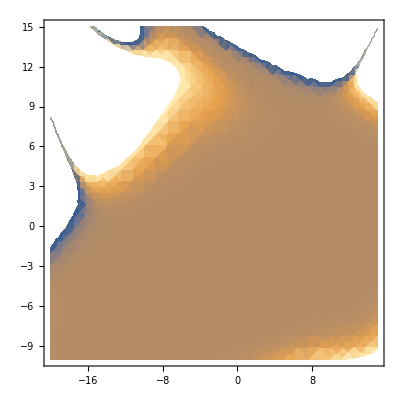

```mathematica
DensityPlot[f[x,y],{x,-20,15},{y,-10,15}]
```

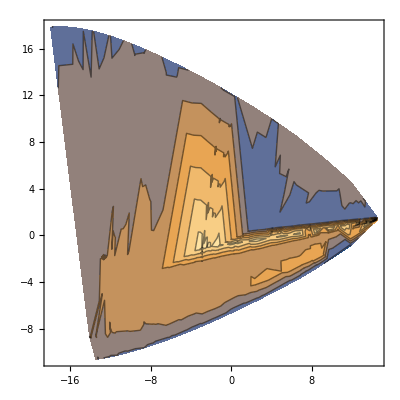

```mathematica
ListContourPlot[data]
```

```mathematica
Color
```